```mathematica
SetDirectory[NotebookDirectory[]];
Get<<"data/SolutionVector2_Dec5.mx";
SolutionVector3=SolutionVector2/.Null->Nothing;
BendTests=Import["data/201708_BendTests_LU_processed_data_Info.mat"];
Bendlabels=Import["data/201708_BendTests_LU_processed_data_Info.mat","Labels"]
BendTestAll=Import["data/201708_BendTests_LU_processed_data_Fw0.mat"];
BendlabelAll=Import["data/201708_BendTests_LU_processed_data_Fw0.mat","Labels"]
force= BendTestAll[[Position[BendlabelAll,"force"][[1,1]] ]];
dflctn= BendTestAll[[Position[BendlabelAll,"dflctn"][[1,1]] ]];
indc= BendTestAll[[Position[BendlabelAll,"indc"][[1,1]] ]];
(*Bstif=Flatten[ BendTests[[Position[Bendlabels,"Bstif"][[1,1]] ]]];(*EI/L^3*)*)
Kcant=Flatten[ BendTests[[Position[Bendlabels,"Kcant"][[1,1]] ]]];
evbool=Flatten[ BendTests[[Position[Bendlabels,"evbool"][[1,1]] ]]];
L=Flatten[ BendTests[[Position[Bendlabels,"L"][[1,1]] ]]];
EffectTestsNo=Flatten@Position[evbool,True];
```

{Bstif,D,E,K_s,Kc_SE,Kcant,L,N_L,Nbranch,Ncycle,SSpattern,evbool,sD,s_L}

{dflctn,dsplcmnt,force,indc}

```mathematica
Outline[text_]:=First@ImportString[ExportString[text,"PDF"],"PDF","TextMode"->"Outlines"]
linearFrameTicks={{Most/@Charting`ScaledTicks[{Identity,Identity}][##]&,Most/@Charting`ScaledFrameTicks[{Identity,Identity}][##]&},{Most/@Charting`ScaledTicks[{Identity,Identity}][##]&,Most/@Charting`ScaledFrameTicks[{Identity,Identity}][##]&}};
```

```mathematica
EffectTestsNo
```

{1,3,12,27,28,29}

```mathematica
ColorData[88]/@Range[3]
```

{Hue[0.42, 0.67, 0.75],Hue[0.17, 1, 0.75],Hue[0.05, 0.7, 1]}

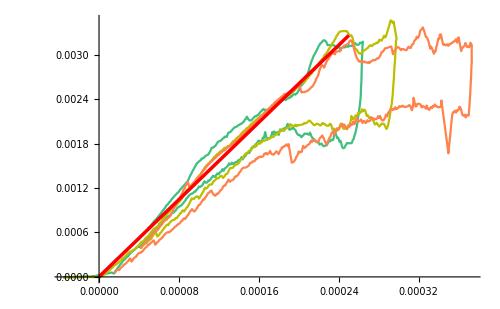
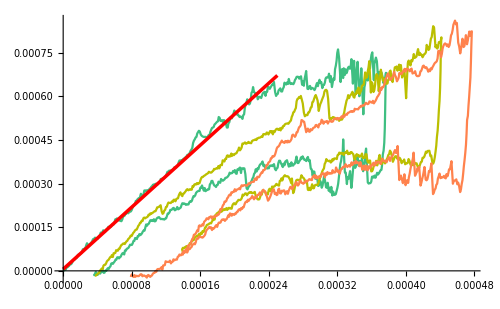
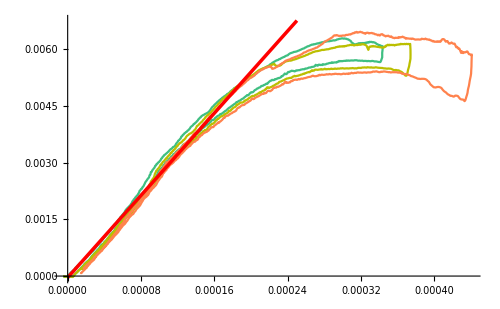
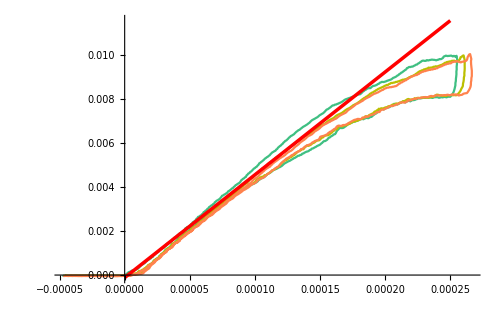
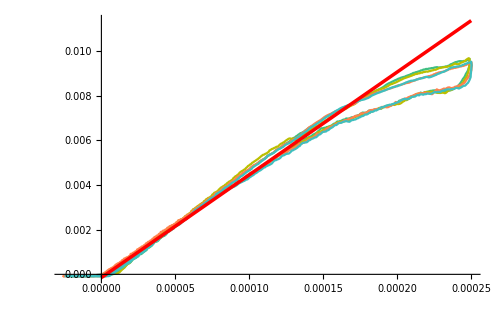
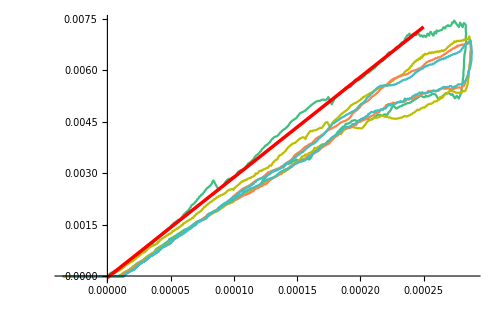
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{{1.7405×10^-6+13.0379 x,5.73912×10^-6+2.66621 x,-0.0000406317+27.1885 x,-0.000115435+46.7573 x,-0.000145662+46.0757 x,-0.0000459035+29.2327 x}}}

```mathematica
result = Reap[Module[{test = # },
cycles=Partition[ReplaceAll[Round[indc[[test]]],0->Nothing],2,1];
data  = Transpose@{dflctn[[test,1;;Round[cycles[[1,2]]/5]]],force[[test,1;;Round[cycles[[1,2]]/5]]]};
line = Fit[data,{1,x},x];
Sow[line];
Show[Append[Table[
EndPoints ={cycles[[2n-1,1]],cycles[[2n,2]]};
ListLinePlot[
Transpose@{dflctn[[test,EndPoints[[1]];;EndPoints[[2]]]],force[[test,EndPoints[[1]];;EndPoints[[2]]]]}
,PlotStyle->ColorData[88][n]
],
{n,(Length@cycles)/2}],
Plot[line,{x,0,0.00025},PlotStyle->{Red,Thickness[0.005]}]],
PlotRange->All,ImageSize->500]
]&/@Range[6]]
```

```mathematica
colorlist ={RGBColor@@({53,144,238}/255),
RGBColor@@({49,195,166}/255),
RGBColor@@({208,190,30}/255)}
```

{RGBColor[Rational[53, 255], Rational[48, 85], Rational[14, 15]],RGBColor[Rational[49, 255], Rational[13, 17], Rational[166, 255]],RGBColor[Rational[208, 255], Rational[38, 51], Rational[2, 17]]}

```mathematica
Bstif= (D[result[[2,1,#]],x]&/@Range[6])/48;
OblSlope=(Kcant[[EffectTestsNo]]/Bstif);
fw0All=Table[{dflctn[[i,j]]/L[[EffectTestsNo]][[i]],force[[i,j]]/Bstif[[i]]/L[[EffectTestsNo]][[i]]},{i,6},{j,Length@force[[i]]}];
fw0Alln0 =ReplaceAll[fw0All,{0.,0.}->Nothing];
```

```mathematica
OblSlope[[5]]
```

124.849

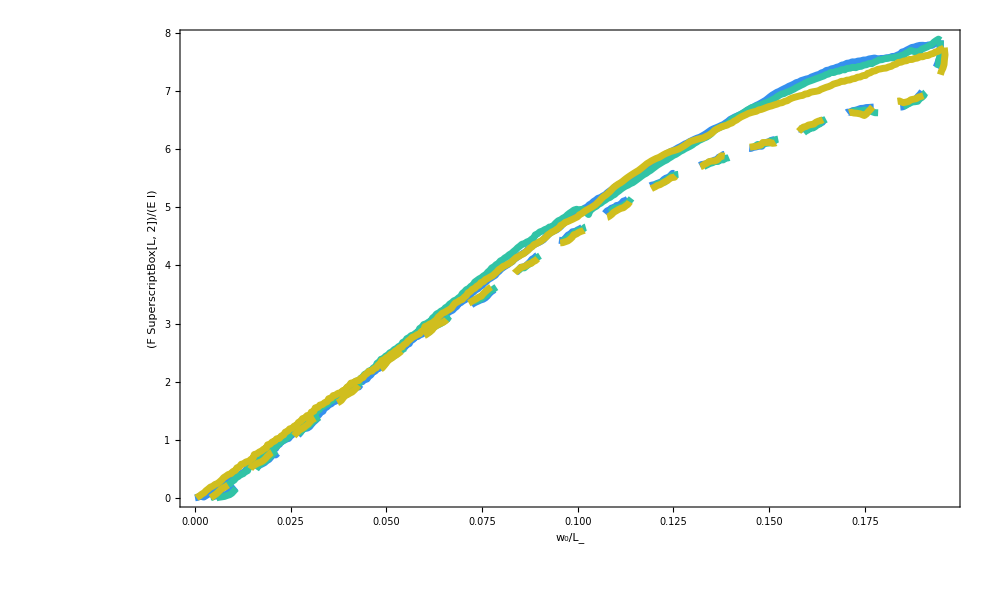

```mathematica
ExpCurve = Module[{test = 5 },
cycles=Partition[ReplaceAll[Round[indc[[test]]],0->Nothing],2,1];
Show[Table[
MidPoints =cycles[[2n-1,2]];
EndPoints ={cycles[[2n-1,1]],cycles[[2n,2]]};
{ListLinePlot[
fw0All[[test,EndPoints[[1]];;MidPoints]]
,PlotStyle->{colorlist[[n]],Thickness[0.005],Opacity[1]},
GridLines->None,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",FontSize->28],
(*FrameTicks->linearFrameTicks,*)FrameLabel->{Style["w_0/L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6,ImageSize->1000],
ListLinePlot[
fw0All[[test,MidPoints;;EndPoints[[2]]]]
,PlotStyle->{Dashing[0.02],colorlist[[n]],Thickness[0.005],Opacity[1]},
GridLines->None,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",FontSize->28],
(*FrameTicks->linearFrameTicks,*)FrameLabel->{Style["w_0/L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6,ImageSize->1000]
},
{n,3}],
PlotRange->All]
]
```

```mathematica
PlotHysterPts[μ0i_:0.5,Ai_:0.05,λi_:0.004π,ϕi_:0,OblSlopei_:30,EndRatio_:0.9]:=Module[{μ0B=μ0i,
Abasis=Ai,
λbasis=λi,
ϕbasis=ϕi,
OblSlope=OblSlopei,
Posμ0B,Endw0,fitFw0B,Levelμ0S,EndFail},
Posμ0B=μ0B/0.002+1;
Endw0=SolutionVector3[[Posμ0B,-1,1]];
fitFw0B=Module[{data1,fit},
data1=SolutionVector3[[Posμ0B,;;,{1,2}]];
fit[x_]=Fit[data1,{x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,Evaluate@fit[x]]
];
Off[General::partw];
Levelμ0S=Module[{μ0=μ0B,A = Abasis,λ=λbasis,ϕ=ϕbasis,arclength,frictionC,levelset,FwLevelset,Levelμ0},
arclength=SolutionVector3[[;;,;;,5]];
frictionC=SolutionVector3[[;;,;;,6]];
levelset=frictionC-μ0(1+A Cos[2π arclength/λ+ϕ]);
FwLevelset=Flatten[Table[{SolutionVector3[[i,j,1]],SolutionVector3[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector3},{j,1,Length[SolutionVector3[[i]]]}],1];
Levelμ0=Select[FwLevelset,Abs[#[[3]]]<10^-3&];
(SortBy[Levelμ0,First])
(*FailIndex=Length@Select[Levelμ0S[[1,;;,1]],0<#≤w0starN[[NTest]]&]+LengthOffset;*)];
EndFail=Round[EndRatio  Length@Levelμ0S];
ListLinePlot[Levelμ0S[[;;EndFail,{1,2}]],PlotStyle->Directive[Red,Thickness[0.0015],Opacity[0.7]],
GridLines->None,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",FontSize->28],
FrameTicks->linearFrameTicks,FrameLabel->{Style["w_0/L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6,ImageSize->1000]
(*The above commands are only for plotting*)
]
```

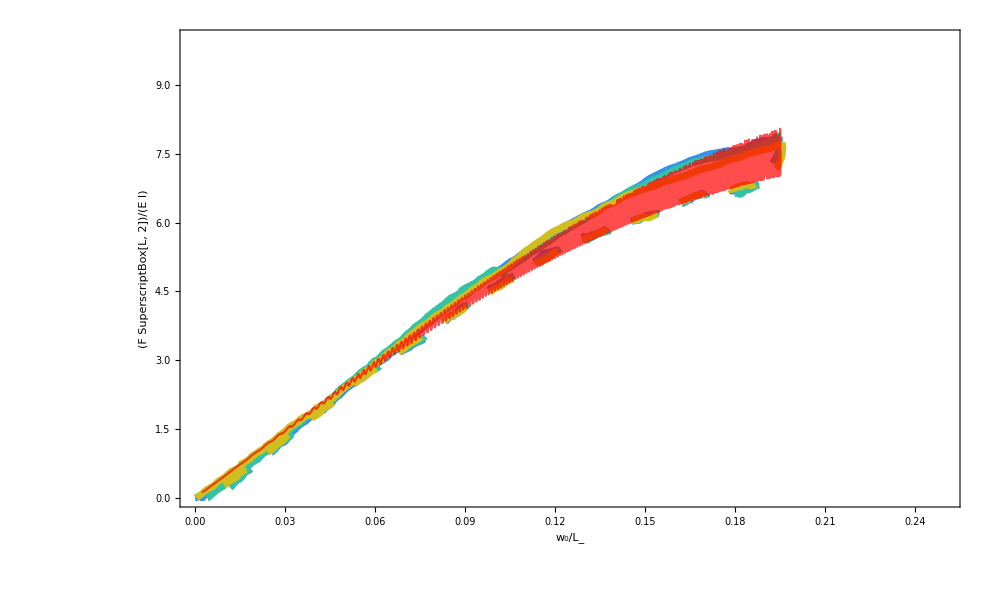

```mathematica
TeoCurve=PlotHysterPts[0.35,0.52,0.00015π,0,OblSlope[[5]],0.724];
CyclingCompare = Show[ExpCurve,TeoCurve,PlotRange->{{0,0.25},{0,10}},ImageSize->1000]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["figure/CyclingCompare.EPS",CyclingCompare,ImageSize->1000]
```

/Users/wenqiangfang/Dropbox (Brown)/Apps/Github/Computational-Solid-Mechanics/ElasticaSolution

figure/CyclingCompare.EPS

```mathematica
SetDirectory[NotebookDirectory[]]
Export["figure/ExpCurve.EPS",ExpCurve,ImageSize->1000]
```

/Users/wenqiangfang/Dropbox (Brown)/Apps/Github/Computational-Solid-Mechanics/ElasticaSolution

figure/ExpCurve.EPS

```mathematica
Export["figure/CyclingCompare.EPS",Import[Export["p5.pdf",CyclingCompare,ImageSize->1000,ImageResolution->1000]],ImageResolution->1000]
```

figure/CyclingCompare.EPS

```mathematica
N@0.00015π
```

0.000471239